-Graphics-

## Lesson 3: Solutions to differential equations

-Graphics-

## Overview

In the previous lesson, two scenarios were described that can be modeled using differential equations.

The falling object model:

m v'(t)=m g-α v(t)

And the population model:

p'(t)=r p(t)-d

Suppose it is necessary to answer questions like: What is the population at any given time? or How long does it take for the population to double?

Answering important questions like this requires the solution to the differential equation:

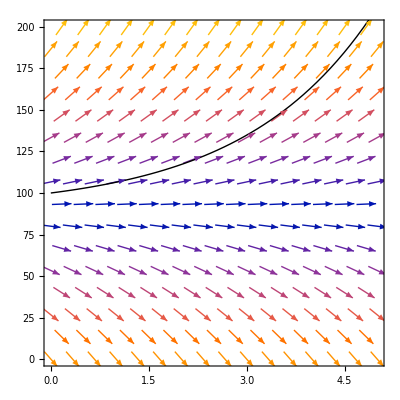

```mathematica
Show[VectorPlot[{1,-45+0.5 p},{t,0,5},{p,0,200}],Plot[90+10*ⅇ^(t/2),{t,0,5},]]
```

## Solutions to Differential Equations

There can be many functions that satisfy a single differential equation.

Consider the differential equation:

y'(x)=1

The solution to this equation is some function that, when differentiated, is equal to one.

There is one immediately obvious answer, y(x)=x:

```mathematica
D[x,x]
```

1

There are actually an infinite number of functions that satisfy this equation, all of which take the form

y(x)=x+C[1],

where C[1] is any number.

In the Wolfram Language, solutions to differential equations can be found with DSolveValue:

```mathematica
DSolveValue[y'[x]==1,y[x],x]
```

x+C[1]

Solutions for more complicated differential equations are not immediately obvious and require the use of calculus or other techniques to solve them.

## Solutions to the Population Model

With parameters r=1/3 and d=30, the population model becomes:

p'(t)=1/3 p(t)-30

Recall some of the qualitative properties of this equation by creating a direction field:

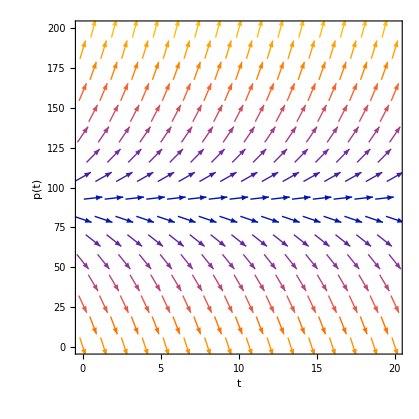

```mathematica
VectorPlot[{1,-30+ 1/3 p},{t,0,20},{p,0,200},]
```

It can be observed that solutions tend to diverge from the solution where the population begins with 90 rabbits.

This information can be useful for verifying results when solving equations.

## Solutions to the Population Model

Find the function that satisfies the given differential equation:

p'(t)=1/3 p(t)-30

The differential equation can be rewritten as:

(ⅆp/ⅆt)/(p(t)-90)=1/3

Move ⅆt to the right-hand side and use Integrate to find an expression involving p(t), where C[1] is an arbitrary constant:

```mathematica
sln=Integrate[1/(p[t]-90),p[t]]==Integrate[1/3,t,GeneratedParameters->C]
```

Log[-90+p[t]]==t/3+C[1]

Finally, the unknown function can be obtained using Solve.

```mathematica
sol=Solve[sln,p[t],Reals]
```

{{p[t]→90+ⅇ^(t/3+C[1])}}

This is an example of solving a differential equation using a technique known as separation of variables, which will be discussed in more detail further on in the course.

## Verify a Solution

Suppose a function is given and it is necessary to verify whether it solves the differential equation.

This can be done by first defining the equation:

```mathematica
eqn =p'[t]==1/3*p[t]-30;
```

Define a function that satisfies the equation:

```mathematica
p[t_]:=90+C[1]*ⅇ^((1/3)t)
```

Applying Simplify to the equation returns True, which proves the function satisfies the equation:

```mathematica
Simplify[eqn]
```

True

## Verify a Solution

The previous method to verify a solution assigns a value to the symbol p that may interfere with future calculations. For example:

```mathematica
DSolveValue[p'[t]==1/3*p[t]-30,p[t],t]
```

DSolveValue[1/3 ⅇ^(t/3) C[1]==-30+1/3 (90+ⅇ^(t/3) C[1]),90+ⅇ^(t/3) C[1],t]

To avoid such conflicts, ReplaceAll (/.) and Function will be used whenever possible throughout this course.

To demonstrate, first apply Clear to the definition assigned to p earlier:

```mathematica
Clear[p]
```

Define the form of the solution:

```mathematica
solution=90+Subscript[C, 1]*Exp[1/3*t];
```

Insert the solution into the equation with ReplaceAll (/.):

```mathematica
verify=(p'[t]==1/3*p[t]-30)/.p->Function[t,Evaluate[solution]]
```

1/3 ⅇ^(t/3) C_1==-30+1/3 (90+ⅇ^(t/3) C_1)

Apply Simplify to verify the solution:

```mathematica
Simplify[verify]
```

True

Since you applied Clear to the symbol p, the previous definition no longer interferes with DSolveValue:

```mathematica
DSolveValue[p'[t]==1/3*p[t]-30,p[t],t]
```

90+ⅇ^(t/3) C[1]

## Initial Value Problems

The general solution as been found to be:

p(t)=90+C[1]e^(t/3)

Frequently, it is important to find a single solution by specifying a value of C_1 to satisfy an initial condition.

For example, the problem could specify that the population is first observed to be at 100 rabbits.

This initial condition can be written as p(0)=100.

Substitute t=0 and p(0)=100 into the equation and use Solve to find the value of C[1] that satisfies this initial condition:

```mathematica
Solve[100==90+Subscript[C, 1],Subscript[C, 1]]
```

{{C_1→10}}

## Initial Value Problems

With the value of C[1]=10, the solution will satisfy the differential equation in addition to the initial condition p(0)=100:

```mathematica
(p'[t]==1/3*p[t]-30)/.p->Function[t,90+10*Exp[t/3]]//Simplify
```

True

Observe the particular solution compared to the direction field:

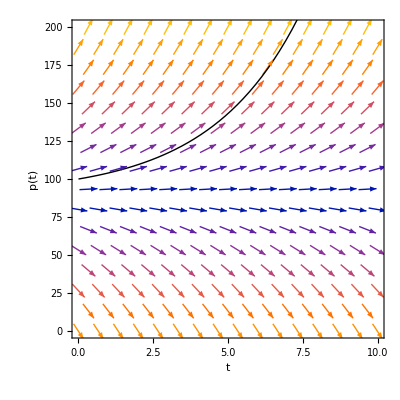

```mathematica
Show[VectorPlot[{1,1/3 p-30},{t,0,10},{p,0,200},],Plot[90+10*Exp[t/3],{t,0,10},]]
```

The slope of the solution matches the slope of each segment in the direction field.

## Initial Value Problem Example

Consider the initial value problem:

p'(t)=1/3 p(t)-30

p(0)=100

Determine the time it takes for the population to double.

The solution to this initial value problem has already been found:

```mathematica
sol=DSolveValue[{p'[t]==1/3*p[t]-30,p[0]==100},p[t],t]//Expand
```

90+10 ⅇ^(t/3)

In order to find the time that is required for the population to double, set the solution equal to twice the initial population and use Solve:

```mathematica
Solve[sol==200,t,Reals]//N
```

{{t→7.19369}}

When t=7.19369, the population has doubled.

## Falling Object Model

With parameters m=50 and α=10, the falling object model becomes:

50v'(t)=50 g-10 v(t)

Below is the corresponding direction field associated with the falling object model:

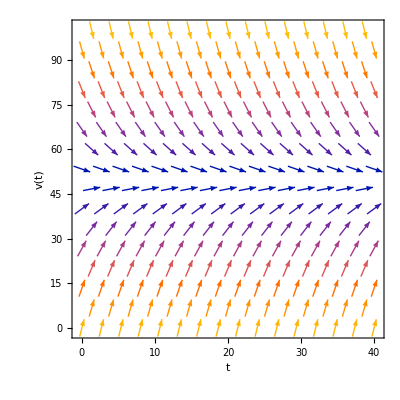

```mathematica
VectorPlot[{1,9.81-v/5},{t,0,40},{v,0,100},]
```

Solutions tend to converge to around v=50, which can be interpreted as the terminal velocity.

## Solution to Falling Object Model

Consider the following initial value problem:

50v'(t)=50 g-10 v(t)

v(0)=0

Just like the population model, this equation can be rewritten as:

(v'(t))/(g-1/5 v(t))=1

Apply Integrate to find an expression involving v(t):

```mathematica
eqn=Integrate[1/(g-1/5 v[t]),v[t]]==Integrate[1,t,GeneratedParameters->C]
```

-5 Log[g-v[t]/5]==t+C[1]

Obtain an expression for the unknown function by solving for v(t), where C_1 is an arbitrary constant determined by the initial conditions:

```mathematica
sol=Solve[eqn,v[t],Reals]//Expand
```

{{v[t]→-5 ⅇ^(-t/5-C[1]/5)+5 g}}

## Solution to Falling Object Model

In order to find the particular solution that satisfies this initial condition, define the general solution:

```mathematica
generalSolution[t_]=Subscript[C, 2] Exp[-t/5]+5 g
```

5 g+ⅇ^(-t/5) C_2

Here, C_2=-5 e^(-C_1/5) is just another arbitrary constant.

Insert t=0 into the general solution and use Solve to find the value of C_2:

```mathematica
constant=Solve[generalSolution[0]==0,Subscript[C, 2]][[1]]
```

{C_2→-5 g}

Thus, the particular solution is:

```mathematica
particularSolution[t_]=(generalSolution[t]/.constant)
```

5 g-5 ⅇ^(-t/5) g

This solution can also be verified by using the function DSolveValue:

```mathematica
DSolveValue[{50 v'[t]==50 g-10 v[t],v[0]==0},v[t],t]//Expand
```

5 g-5 ⅇ^(-t/5) g

## Summary

Some differential equations can be solved through straightforward integration.

When an initial condition is specified, there is a unique solution to a first-order differential equation.

Qualitative conclusions on the behavior of solutions to differential equations can largely be made from the direction field.

In order to answer quantitative questions about a specific solution, it is helpful to solve that associated initial value problem.

The next lesson will cover the classification of differential equations.